```mathematica
w[r_]:=c3*r^2+c4;
```

```mathematica
M[r_]:=-d*(D[w[r],{r,2}]+ν/r D[w[r],r]);
```

```mathematica
Simplify[M[r]]
```

-2 c3 d (1+ν)

Moment boundary condition at r=rmax:

```mathematica
Solve[-2 c3 d (1+ν)==T*g,c3]
```

{{c3→-(g T)/(2 d (1+ν))}}

Displacement boundary condition at r=rmax:

```mathematica
Solve[-(g T)/(2 d (1+ν))*rmax^2+c4==0,c4]
```

{{c4→(g rmax^2 T)/(2 d (1+ν))}}

```mathematica
wsol[r_]:=-(g T)/(2 d (1+ν))*r^2+(g rmax^2 T)/(2 d (1+ν));
```

Max deflection at center:

```mathematica
wmax=wsol[0]
```

(g rmax^2 T)/(2 d (1+ν))

```mathematica
Simplify[(g (dmax/2)^2 T)/(2 d (1+ν))]
```

(dmax^2 g T)/(8 d+8 d ν)

Back out required bending stiffness for small deflections:

```mathematica
Solve[wmax/h==0.2,d]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{d→(2.5 g rmax^2 T)/(h (1.+ν))}}

Back out required triangle sidelength of tetrahedral truss:

```mathematica
Solve[(2.5 g rmax^2 T)/(h (1.+ν))==Sqrt[3]/4*(ewire*awire*lwire),lwire]
```

{{lwire→(5.7735 g rmax^2 T)/(awire ewire h (1.+ν))}}

```mathematica
lwire=(5.773502691896258 g rmax^2 T)/(awire ewire h (1.+ν));
```

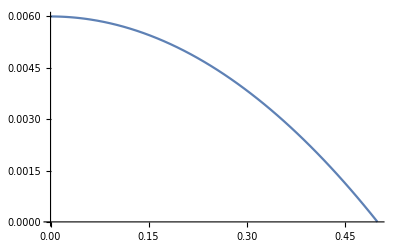

lwire

```mathematica
g=0.05; (*5 cm gap*)
rmax=0.5;(*1 m diameter plate*)
h=0.03;(*thickness of plate*);
T=100;(*10 N/m mesh tension*)
awire=π*0.0005^2; (*1 mm diameter wire*)
ewire=200*10^9; (*Steel*)
ν=0.3;
d=(2.5 g rmax^2 T)/(h (1.+ν));
Plot[-(g T)/(2 d (1+ν))*r^2+(g rmax^2 T)/(2 d (1+ν)),{r,0,rmax}]
Simplify[lwire]
ClearAll[g,rmax,h,T,awire,ewire,ν,d]
```

Maximum allowable separation from Lang paper:

```mathematica
Sqrt[(π d^2)/(2 Sqrt[3]*n)]
```

(√(1/n) √(π/2))/3^(1/4)

```mathematica
d=1;
Solve[Sqrt[(π d^2)/(2 Sqrt[3]*n)]==0.1,n]
Clear[d]
```

{{n→90.69}}